```mathematica
(*Radius of Sphere one*)
r1=1.;
(*Radius of Sphere two*)
r2=1.;
(*Distance between the centres of the spheres*)
R=3.5;
(*NN is the maximal ell in the basis of vector-spherical harmonics*)
logdet[λλ_,NN_]:=(
(*value of lambda, not here real values correspond to the positive imaginary line*)
λ=λλ;
(*unit rotational vector field theta*)
vecθ={Cos[θ]Cos[ϕ],Cos[θ]Sin[ϕ],-Sin[θ]};
(*unit rotational vector field phi*)
vecϕ={-Sin[ϕ],Cos[ϕ],0};
(*radius vector on sphere one*)
rad=r1{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
(*radius vector on sphere two*)
radp=r2{Sin[θp]Cos[ϕp],Sin[θp]Sin[ϕp], Cos[θp]}+{0,0,R};
(*vector spherical harmonics on  sphere one*)
(*t1 is the spherical harmonic U and Psi; t2 corresponds to Vm and Phi*)
(*note that these form an orthonormal basis on the unit sphere*)
t1[ell_,m_]=1/Sqrt[ell(ell+1)](D[SphericalHarmonicY[ell,m,θ,ϕ],θ]vecθ+1/Sin[θ]D[SphericalHarmonicY[ell,m,θ,ϕ],ϕ]vecϕ);
t2[ell_,m_]=1/Sqrt[ell(ell+1)](D[SphericalHarmonicY[ell,m,θ,ϕ],θ]vecϕ-1/Sin[θ]D[SphericalHarmonicY[ell,m,θ,ϕ],ϕ]vecθ);
(*vector spherical harmonics on  sphere two*)
(*these are the same as on sphere one, but the angle names are primed*)
t1p[ell_,m_]=t1[ell,m]/.{θ->θp,ϕ->ϕp};
t2p[ell_,m_]=t2[ell,m]/.{θ->θp,ϕ->ϕp};
(*merge basis functions into one by choosing polarization index pol *)
basis[ell_,m_,pol_]:=(If[pol==1,ans=t1[ell,m]];If[pol==2,ans=t2[ell,m]];ans);
basisp[ell_,m_,pol_]:=(If[pol==1,ans=t1p[ell,m]];If[pol==2,ans=t2p[ell,m]];ans);
(*List of possible indices for the vector spherical harmonics in format (ell,m,p)*)
indexlist=Flatten[Table[Table[Table[{ell,m,pol},{pol,1,2}],{m,-ell,ell}],{ell,1,NN}],2];
(*index the list by natural numbers*)
mp[k_]:=indexlist[[k]];
(*Computation of the Matrix-Green's function*)
dxxp=Sqrt[(x-xp)^2+(y-yp)^2+(z-zp)^2];
(*scalar Greens function*)
scgreen[rr_]=(Exp[λ I rr])/(4 Pi rr);
Mgreen=Simplify[{Curl[Curl[scgreen[dxxp]{1,0,0},{xp,yp,zp}],{xp,yp,zp}],Curl[Curl[scgreen[dxxp]{0,1,0},{xp,yp,zp}],{xp,yp,zp}],Curl[Curl[scgreen[dxxp]{0,0,1},{xp,yp,zp}],{xp,yp,zp}]}];
(*For comparision the dyadic version*)
Dgreen=Simplify[IdentityMatrix[3]scgreen[dxxp]λ^2+{Grad[Div[scgreen[dxxp]{1,0,0},{xp,yp,zp}],{xp,yp,zp}],Grad[Div[scgreen[dxxp]{0,1,0},{xp,yp,zp}],{xp,yp,zp}],Grad[Div[scgreen[dxxp]{0,0,1},{xp,yp,zp}],{xp,yp,zp}]}];
(*the kernel function expressed in spherical coordinates on the two spheres*)
kerfun=Dgreen/.{x->rad[[1]],y->rad[[2]],z->rad[[3]],xp->radp[[1]],yp->radp[[2]],zp->radp[[3]]};
(*cofficients needed for the expansion into spherical plane waves*)
γbessel[ell_,rr_]=(SphericalBesselJ[ell,λ rr]/(D[rr SphericalBesselJ[ell,λ rr],rr]/rr));
γhankel[ell_,rr_]=(SphericalHankelH1[ell,λ rr]/(D[rr SphericalHankelH1[ell,λ rr],rr]/rr));
(*Part to compute the diagonal part. We start with the maps Λ plus and minus*)
Λtwplus1[k1_,k2_]:=(ind1=mp[k1];
ind2=mp[k2];
elll=ind1[[1]];
If[(ind1[[1]]==ind2[[1]]) && (ind1[[2]]==ind2[[2]])&& (ind1[[3]]==ind2[[3]])&& (ind1[[3]]==1),result=I(γbessel[elll,r1]λ),result=0.];
If[(ind1[[1]]==ind2[[1]]) && (ind1[[2]]==ind2[[2]])&& (ind1[[3]]==ind2[[3]])&& (ind1[[3]]==2),result=-I /(γbessel[elll,r1] λ)];
result);
Λtwminus1[k1_,k2_]:=(ind1=mp[k1];
ind2=mp[k2];
elll=ind1[[1]];
If[(ind1[[1]]==ind2[[1]]) && (ind1[[2]]==ind2[[2]])&& (ind1[[3]]==ind2[[3]])&& (ind1[[3]]==1),result=I(γhankel[elll,r1]λ),result=0.];
If[(ind1[[1]]==ind2[[1]]) && (ind1[[2]]==ind2[[2]])&& (ind1[[3]]==ind2[[3]])&& (ind1[[3]]==2),result=-I/(γhankel[elll,r1]λ)];
result);
MatDiag1=Inverse[Table[I λ^(-1)(Λtwplus1[k1,k2]-Λtwminus1[k1,k2]),{k1,1,Length[indexlist]},{k2,1,Length[indexlist]}]];
MatOffDiag[k1_,k2_]:=(
ind1=mp[k1];
ind2=mp[k2];
If[ind1[[2]]==ind2[[2]],result=2Pi Quiet[NIntegrate[Conjugate[basis[ind1[[1]],ind1[[2]],ind1[[3]]]].kerfun.basisp[ind2[[1]],ind2[[2]],ind2[[3]]]*Sin[θ]Sin[θp]/.{ϕp->0.},{θ,0,Pi},{ϕ,0,2Pi},{θp,0,Pi},Method->"MultiPeriodic",AccuracyGoal->5]],result=0.];result);
MM=Length[indexlist];
A =MatDiag1;
B=ParallelTable[MatOffDiag[j,k],{k,1,MM},{j,1,MM}];
Log[Det[IdentityMatrix[MM]-Inverse[A].Transpose[B].Inverse[A].B]]);
```

```mathematica
logdet[0.001 I,6]
```

-0.00684647-1.72421×10^-19 ⅈ

{0.01,-0.00672924+2.76482×10^-21 ⅈ}

{0.11,-0.00664533+4.23108×10^-19 ⅈ}

{0.21,-0.00642418-4.63578×10^-19 ⅈ}

{0.31,-0.00604554-4.63822×10^-20 ⅈ}

{0.41,-0.00551439-3.61233×10^-20 ⅈ}

{0.51,-0.00487554+3.13789×10^-19 ⅈ}

{0.61,-0.00419073-4.83782×10^-20 ⅈ}

{0.71,-0.00351596+1.79275×10^-19 ⅈ}

{0.81,-0.00289088-6.07006×10^-20 ⅈ}

{0.91,-0.00233773+3.75913×10^-20 ⅈ}

{1.01,-0.00186479-1.52926×10^-20 ⅈ}

{1.11,-0.00147092+5.85235×10^-20 ⅈ}

{1.21,-0.00114951+3.15094×10^-20 ⅈ}

{1.31,-0.000891404-6.67415×10^-21 ⅈ}

{1.41,-0.00068678+1.49838×10^-22 ⅈ}

{1.51,-0.000526227-8.91357×10^-21 ⅈ}

{1.61,-0.00040132-1.00377×10^-20 ⅈ}

{1.71,-0.000304828+1.58281×10^-21 ⅈ}

{1.81,-0.000230727+1.65329×10^-21 ⅈ}

{1.91,-0.000174107-1.64673×10^-21 ⅈ}

{2.01,-0.000131029-4.69742×10^-22 ⅈ}

{2.11,-0.000098375+3.68704×10^-22 ⅈ}

{2.21,-0.0000737031-1.95483×10^-22 ⅈ}

{2.31,-0.0000551147-4.8899×10^-23 ⅈ}

{2.41,-0.0000411446+3.67118×10^-23 ⅈ}

{2.51,-0.0000306687-5.95357×10^-23 ⅈ}

{2.61,-0.0000228285+3.87731×10^-24 ⅈ}

{2.71,-0.0000169713+4.86464×10^-23 ⅈ}

{2.81,-0.0000126026-1.1733×10^-23 ⅈ}

{2.91,-9.34865×10^-6+2.81805×10^-23 ⅈ}

{3.01,-6.92829×10^-6+1.88315×10^-23 ⅈ}

{3.11,-5.13008×10^-6+7.29647×10^-24 ⅈ}

{3.21,-3.79555×10^-6+1.78043×10^-23 ⅈ}

{3.31,-2.80612×10^-6+2.31419×10^-24 ⅈ}

{3.41,-2.0732×10^-6-4.65114×10^-24 ⅈ}

{3.51,-1.53076×10^-6+6.69496×10^-25 ⅈ}

{3.61,-1.12959×10^-6+3.47583×10^-24 ⅈ}

{3.71,-8.33108×10^-7+6.07418×10^-25 ⅈ}

{3.81,-6.14143×10^-7+4.38868×10^-25 ⅈ}

{3.91,-4.52521×10^-7-1.62846×10^-24 ⅈ}

InterpolatingFunction::dmval: Input value {0.0000817143} lies outside the range of data in the interpolating function. Extrapolation will be used.

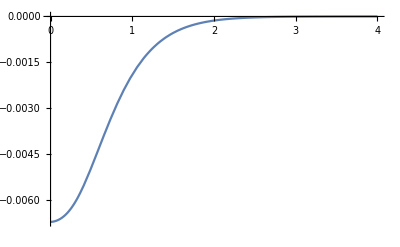

InterpolatingFunction::dmvali: The integration endpoint 0 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmvali: The integration endpoint 4 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.00546936+5.38748×10^-20 ⅈ

```mathematica
tbl={};
Do[
{val=logdet[I lam,6],AppendTo[tbl,{lam,val}],Print[{lam,val}]},{lam,0.001,5,0.1}]
f=Interpolation[tbl,InterpolationOrder->3];
Plot[f[lam],{lam,0.0,4}]
NIntegrate[f[lam],{lam,0,4}]
```

```mathematica
0.00268299/Pi
```

0.000854022

```mathematica
A =MatDiag1;
B=ParallelTable[MatOffDiag[j,k],{k,1,MM},{j,1,MM}];
z=IdentityMatrix[MM]*0;
R=ArrayFlatten[{{A,B},{ConjugateTranspose[B],A}}].Inverse[ArrayFlatten[{{A,Transpose[z]},{z,A}}]]
Log[Det[IdentityMatrix[MM]-Inverse[A].ConjugateTranspose[B].Inverse[A].B]]
Log[Det[R]]
```